```mathematica
data = EntityValue["Country", "BorderingCountries", "EntityAssociation"];
```

```mathematica
vertices = Keys[data];
```

```mathematica
edges = UndirectedEdge @@@ Flatten[Thread /@ Normal[data]];
```

```mathematica
graph = SimpleGraph[Graph[vertices, edges]]
```

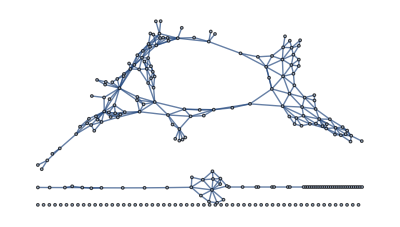

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
Length[components]
```

91

```mathematica
components = ConnectedComponents[graph]
```

{{Afghanistan,Iran,China,Pakistan,Tajikistan,Turkmenistan,Uzbekistan,Iraq,Azerbaijan,Turkey,Armenia,India,Kyrgyzstan,Laos,North Korea,Russia,Vietnam,Nepal,Mongolia,Bhutan,Kazakhstan,Myanmar,Kuwait,Syria,Saudi Arabia,Jordan,Georgia,Bulgaria,Greece,Bangladesh,Cambodia,Thailand,South Korea,Finland,Latvia,Lithuania,Belarus,Estonia,Poland,Norway,Ukraine,Israel,Lebanon,Oman,Qatar,United Arab Emirates,Yemen,West Bank,North Macedonia,Serbia,Romania,Albania,Malaysia,Sweden,Czech Republic,Slovakia,Germany,Hungary,Moldova,Gaza Strip,Egypt,Kosovo,Bosnia and Herzegovina,Croatia,Montenegro,Brunei,Indonesia,Austria,Belgium,Denmark,France,Luxembourg,Netherlands,Switzerland,Slovenia,Libya,Sudan,Papua New Guinea,East Timor,Liechtenstein,Italy,Andorra,Spain,Monaco,Algeria,Tunisia,Niger,Chad,South Sudan,Eritrea,Central African Republic,Ethiopia,San Marino,Vatican City,Gibraltar,Morocco,Portugal,Mali,Mauritania,Western Sahara,Benin,Nigeria,Burkina Faso,Cameroon,Democratic Republic of the Congo,Uganda,Kenya,Djibouti,Republic of the Congo,Somalia,Guinea,Ivory Coast,Senegal,Togo,Ghana,Equatorial Guinea,Gabon,Angola,Rwanda,Tanzania,Zambia,Burundi,Sierra Leone,Guinea-Bissau,Liberia,Gambia,Namibia,Mozambique,Malawi,Botswana,Zimbabwe,South Africa,Eswatini,Lesotho},{Uruguay,Brazil,Argentina,Bolivia,French Guiana,Paraguay,Suriname,Venezuela,Colombia,Guyana,Peru,Chile,Ecuador,Panama,Costa Rica,Nicaragua,Honduras,Guatemala,El Salvador,Belize,Mexico,United States,Canada},{Missing[NotApplicable],Hong Kong,Macau},{United Kingdom,Ireland},{Haiti,Dominican Republic},{Sint Maarten,Saint Martin},{South Georgia and the South Sandwich Islands},{Cyprus},{Mayotte},{American Samoa},{Niue},{Tuvalu},{Marshall Islands},{Cayman Islands},{Greenland},{Maldives},{Nauru},{Caribbean Netherlands},{Anguilla},{Cocos Keeling Islands},{Réunion},{Bouvet Island},{Samoa},{Iceland},{Kiribati},{Saint Helena, Ascension and Tristan da Cunha},{Montserrat},{Japan},{Barbados},{Turks and Caicos Islands},{Malta},{Cape Verde},{São Tomé and Príncipe},{Bermuda},{Cook Islands},{New Caledonia},{Fiji},{French Southern And Antarctic lands},{Saint Barthelemy},{French Polynesia},{Saint Lucia},{Guam},{Faroe Islands},{Comoros},{Jersey},{Wallis and Futuna Islands},{Aland Islands},{Tokelau},{British Indian Ocean Territory},{Saint Kitts and Nevis},{Madagascar},{Bahamas},{Micronesia},{Guadeloupe},{Curacao},{Grenada},{Australia},{Solomon Islands},{Martinique},{British Virgin Islands},{Saint Vincent and the Grenadines},{Cuba},{Bahrain},{Puerto Rico},{Saint Pierre and Miquelon},{Guernsey},{Antarctica},{Christmas Island},{Mauritius},{United States Virgin Islands},{Vanuatu},{Trinidad and Tobago},{Aruba},{Norfolk Island},{Seychelles},{Dominica},{Isle of Man},{Philippines},{Taiwan},{Jamaica},{Northern Mariana Islands},{Antigua and Barbuda},{Svalbard},{Sri Lanka},{Falkland Islands},{Pitcairn Islands},{New Zealand},{Palau},{Tonga},{United States Minor Outlying Islands},{Singapore}}

```mathematica
AfroEurAsia = components[[1]]
```

{Afghanistan,Iran,China,Pakistan,Tajikistan,Turkmenistan,Uzbekistan,Iraq,Azerbaijan,Turkey,Armenia,India,Kyrgyzstan,Laos,North Korea,Russia,Vietnam,Nepal,Mongolia,Bhutan,Kazakhstan,Myanmar,Kuwait,Syria,Saudi Arabia,Jordan,Georgia,Bulgaria,Greece,Bangladesh,Cambodia,Thailand,South Korea,Finland,Latvia,Lithuania,Belarus,Estonia,Poland,Norway,Ukraine,Israel,Lebanon,Oman,Qatar,United Arab Emirates,Yemen,West Bank,North Macedonia,Serbia,Romania,Albania,Malaysia,Sweden,Czech Republic,Slovakia,Germany,Hungary,Moldova,Gaza Strip,Egypt,Kosovo,Bosnia and Herzegovina,Croatia,Montenegro,Brunei,Indonesia,Austria,Belgium,Denmark,France,Luxembourg,Netherlands,Switzerland,Slovenia,Libya,Sudan,Papua New Guinea,East Timor,Liechtenstein,Italy,Andorra,Spain,Monaco,Algeria,Tunisia,Niger,Chad,South Sudan,Eritrea,Central African Republic,Ethiopia,San Marino,Vatican City,Gibraltar,Morocco,Portugal,Mali,Mauritania,Western Sahara,Benin,Nigeria,Burkina Faso,Cameroon,Democratic Republic of the Congo,Uganda,Kenya,Djibouti,Republic of the Congo,Somalia,Guinea,Ivory Coast,Senegal,Togo,Ghana,Equatorial Guinea,Gabon,Angola,Rwanda,Tanzania,Zambia,Burundi,Sierra Leone,Guinea-Bissau,Liberia,Gambia,Namibia,Mozambique,Malawi,Botswana,Zimbabwe,South Africa,Eswatini,Lesotho}

```mathematica
SetAttributes[UndirectedEdge,Orderless];
```

```mathematica
edgeList[x_]:=(UndirectedEdge[x,#] &)/@AdjacencyList[subgraph, x, 2]
```

```mathematica
edges =  DeleteDuplicates[Flatten[edgeList/@AfroEurAsia,1]];
```

AdjacencyList::graph: A graph object is expected at position 1 in AdjacencyList[subgraph<->Afghanistan,Afghanistan<->Afghanistan,2<->Afghanistan].

AdjacencyList::graph: A graph object is expected at position 1 in AdjacencyList[subgraph<->Iran,Iran<->Iran,2<->Iran].

AdjacencyList::graph: A graph object is expected at position 1 in AdjacencyList[subgraph<->China,China<->China,2<->China].

General::stop: Further output of AdjacencyList::graph will be suppressed during this calculation.

```mathematica
subgraphSquared = Graph[AfroEurAsia, edges];
```

```mathematica
IncidenceList[subgraphSquared, Entity["Country","Afghanistan"]]
```

{Afghanistan<->Iran,Afghanistan<->China,Afghanistan<->Pakistan,Afghanistan<->Tajikistan,Afghanistan<->Turkmenistan,Afghanistan<->Uzbekistan,Afghanistan<->Iraq,Afghanistan<->Azerbaijan,Afghanistan<->Turkey,Afghanistan<->Armenia,Afghanistan<->India,Afghanistan<->Kyrgyzstan,Afghanistan<->Laos,Afghanistan<->North Korea,Afghanistan<->Russia,Afghanistan<->Vietnam,Afghanistan<->Nepal,Afghanistan<->Mongolia,Afghanistan<->Bhutan,Afghanistan<->Kazakhstan,Afghanistan<->Myanmar}

```mathematica
subgraphSquared = SimpleGraph[subgraphSquared]
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of SimpleGraph[subgraphSquared].

Hold[SimpleGraph[subgraphSquared]]

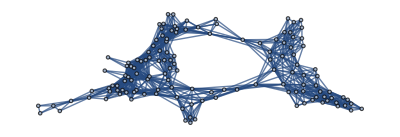

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
edges = EdgeList[subgraphSquared];
```

```mathematica
Save["edgelist.m",edges];
```

```mathematica
FindHamiltonianPath[subgraphSquared]
```

```mathematica
pos = CountryData[#, "CenterCoordinates"] &/@ AfroEurAsia;
```

```mathematica
FindShortestTour[pos, 132, 83]
```

{829.266,{132,134,133,128,129,121,131,130,127,118,109,117,116,104,102,87,76,88,91,105,119,122,120,107,106,89,77,92,90,108,110,47,25,45,46,44,1,4,12,18,20,30,22,32,14,17,31,53,66,67,79,78,33,15,3,19,16,13,5,21,7,6,2,23,8,9,11,27,10,24,43,26,48,60,42,61,29,52,49,62,28,51,59,41,37,36,35,38,34,54,40,70,57,72,73,69,71,82,84,74,80,68,55,39,56,58,50,65,63,64,75,93,81,94,86,85,98,103,101,114,115,112,125,123,111,124,126,113,99,100,96,95,97,83}}

```mathematica
AfroEurAsia[[#]]&/@ {132,134,133,128,129,121,131,130,127,118,109,117,116,104,102,87,76,88,91,105,119,122,120,107,106,89,77,92,90,108,110,47,25,45,46,44,1,4,12,18,20,30,22,32,14,17,31,53,66,67,79,78,33,15,3,19,16,13,5,21,7,6,2,23,8,9,11,27,10,24,43,26,48,60,42,61,29,52,49,62,28,51,59,41,37,36,35,38,34,54,40,70,57,72,73,69,71,82,84,74,80,68,55,39,56,58,50,65,63,64,75,93,81,94,86,85,98,103,101,114,115,112,125,123,111,124,126,113,99,100,96,95,97,83}
```

{South Africa,Lesotho,Eswatini,Mozambique,Malawi,Zambia,Zimbabwe,Botswana,Namibia,Angola,Republic of the Congo,Gabon,Equatorial Guinea,Cameroon,Nigeria,Niger,Libya,Chad,Central African Republic,Democratic Republic of the Congo,Rwanda,Burundi,Tanzania,Kenya,Uganda,South Sudan,Sudan,Ethiopia,Eritrea,Djibouti,Somalia,Yemen,Saudi Arabia,Qatar,United Arab Emirates,Oman,Afghanistan,Pakistan,India,Nepal,Bhutan,Bangladesh,Myanmar,Thailand,Laos,Vietnam,Cambodia,Malaysia,Brunei,Indonesia,East Timor,Papua New Guinea,South Korea,North Korea,China,Mongolia,Russia,Kyrgyzstan,Tajikistan,Kazakhstan,Uzbekistan,Turkmenistan,Iran,Kuwait,Iraq,Azerbaijan,Armenia,Georgia,Turkey,Syria,Lebanon,Jordan,West Bank,Gaza Strip,Israel,Egypt,Greece,Albania,North Macedonia,Kosovo,Bulgaria,Romania,Moldova,Ukraine,Belarus,Lithuania,Latvia,Estonia,Finland,Sweden,Norway,Denmark,Germany,Luxembourg,Netherlands,Belgium,France,Andorra,Monaco,Switzerland,Liechtenstein,Austria,Czech Republic,Poland,Slovakia,Hungary,Serbia,Montenegro,Bosnia and Herzegovina,Croatia,Slovenia,San Marino,Italy,Vatican City,Tunisia,Algeria,Mali,Burkina Faso,Benin,Togo,Ghana,Ivory Coast,Liberia,Sierra Leone,Guinea,Guinea-Bissau,Gambia,Senegal,Mauritania,Western Sahara,Morocco,Gibraltar,Portugal,Spain}

```mathematica
GeoGraphics[{Thick, Red, GeoPath[pos[[Last[%]]]]}]
```

-Graphics-

-Graphics-

```mathematica
interestingPath ={"Brunei","Indonesia","East Timor","Papua New Guinea","Malaysia","Thailand","Bangladesh","Nepal","Afghanistan","Laos","Cambodia","Myanmar","Vietnam","Mongolia","Bhutan","Tajikistan","North Korea","Latvia","Norway","Sweden","Finland","China","South Korea","Russia","Uzbekistan","Turkmenistan","Kyrgyzstan","India","Pakistan","Kazakhstan","Azerbaijan","Lithuania","Estonia","Belarus","Georgia","Poland","Ukraine","Czech Republic","Germany","Monaco","Luxembourg","Spain","Andorra","Gibraltar","Portugal","France","Belgium","Denmark","Netherlands","Switzerland","Liechtenstein","Austria","Vatican City","San Marino","Italy","Slovenia","Romania","Moldova","Bulgaria","Kosovo","Hungary","Slovakia","Croatia","Albania","Turkey","North Macedonia","Montenegro","Bosnia and Herzegovina","Serbia","Greece","Armenia","Iran","Kuwait","Iraq","Israel","Saudi Arabia","United Arab Emirates","Yemen","Oman","Qatar","Jordan","West Bank","Syria","Lebanon","Gaza Strip","Egypt","South Sudan","Ethiopia","Eritrea","Somalia","Uganda","Kenya","Djibouti","Sudan","Central African Republic","Burundi","Malawi","Zimbabwe","South Africa","Lesotho","Eswatini","Botswana","Namibia","Tanzania","Democratic Republic of the Congo","Angola","Mozambique","Zambia","Rwanda","Republic of the Congo","Gabon","Nigeria","Cameroon","Equatorial Guinea","Chad","Benin","Libya","Tunisia","Western Sahara","Morocco","Algeria","Senegal","Sierra Leone","Guinea","Liberia","Ghana","Ivory Coast","Mali","Niger","Togo","Burkina Faso","Mauritania","Guinea-Bissau","Gambia"}
```

{Brunei,Indonesia,East Timor,Papua New Guinea,Malaysia,Thailand,Bangladesh,Nepal,Afghanistan,Laos,Cambodia,Myanmar,Vietnam,Mongolia,Bhutan,Tajikistan,North Korea,Latvia,Norway,Sweden,Finland,China,South Korea,Russia,Uzbekistan,Turkmenistan,Kyrgyzstan,India,Pakistan,Kazakhstan,Azerbaijan,Lithuania,Estonia,Belarus,Georgia,Poland,Ukraine,Czech Republic,Germany,Monaco,Luxembourg,Spain,Andorra,Gibraltar,Portugal,France,Belgium,Denmark,Netherlands,Switzerland,Liechtenstein,Austria,Vatican City,San Marino,Italy,Slovenia,Romania,Moldova,Bulgaria,Kosovo,Hungary,Slovakia,Croatia,Albania,Turkey,North Macedonia,Montenegro,Bosnia and Herzegovina,Serbia,Greece,Armenia,Iran,Kuwait,Iraq,Israel,Saudi Arabia,United Arab Emirates,Yemen,Oman,Qatar,Jordan,West Bank,Syria,Lebanon,Gaza Strip,Egypt,South Sudan,Ethiopia,Eritrea,Somalia,Uganda,Kenya,Djibouti,Sudan,Central African Republic,Burundi,Malawi,Zimbabwe,South Africa,Lesotho,Eswatini,Botswana,Namibia,Tanzania,Democratic Republic of the Congo,Angola,Mozambique,Zambia,Rwanda,Republic of the Congo,Gabon,Nigeria,Cameroon,Equatorial Guinea,Chad,Benin,Libya,Tunisia,Western Sahara,Morocco,Algeria,Senegal,Sierra Leone,Guinea,Liberia,Ghana,Ivory Coast,Mali,Niger,Togo,Burkina Faso,Mauritania,Guinea-Bissau,Gambia}

```mathematica
ConnectedComponents[VertexDelete[g, Entity["Country","Russia"]]]
```

{{Afghanistan,Iran,China,Pakistan,Tajikistan,Turkmenistan,Uzbekistan,Iraq,Azerbaijan,Turkey,Armenia,India,Kyrgyzstan,Laos,North Korea,Vietnam,Nepal,Mongolia,Bhutan,Kazakhstan,Myanmar,Kuwait,Syria,Saudi Arabia,Jordan,Georgia,Bulgaria,Greece,Bangladesh,Cambodia,Thailand,South Korea,Israel,Lebanon,Oman,Qatar,United Arab Emirates,Yemen,West Bank,North Macedonia,Serbia,Romania,Albania,Malaysia,Gaza Strip,Egypt,Kosovo,Hungary,Bosnia and Herzegovina,Croatia,Montenegro,Ukraine,Moldova,Brunei,Indonesia,Libya,Sudan,Slovakia,Austria,Slovenia,Belarus,Poland,Papua New Guinea,East Timor,Algeria,Tunisia,Niger,Chad,South Sudan,Eritrea,Central African Republic,Ethiopia,Czech Republic,Germany,Switzerland,Liechtenstein,Italy,Latvia,Lithuania,Morocco,Mali,Mauritania,Western Sahara,Benin,Nigeria,Burkina Faso,Cameroon,Democratic Republic of the Congo,Uganda,Kenya,Djibouti,Republic of the Congo,Somalia,Belgium,Denmark,France,Luxembourg,Netherlands,San Marino,Vatican City,Estonia,Spain,Guinea,Ivory Coast,Senegal,Togo,Ghana,Equatorial Guinea,Gabon,Angola,Rwanda,Tanzania,Zambia,Burundi,Andorra,Monaco,Gibraltar,Portugal,Sierra Leone,Guinea-Bissau,Liberia,Gambia,Namibia,Mozambique,Malawi,Botswana,Zimbabwe,South Africa,Eswatini,Lesotho},{Finland,Norway,Sweden}}

```mathematica
pos = CountryData[#, "CenterCoordinates"] &/@ interestingPath;
```

```mathematica
GeoGraphics[{Thick, Red, GeoPath[pos]}]
```

-Graphics-

```mathematica
-Graphics-LinguisticAssistant
```

```mathematica
Americas = components[[2]]
```

{Uruguay,Brazil,Argentina,Bolivia,French Guiana,Paraguay,Suriname,Venezuela,Colombia,Guyana,Peru,Chile,Ecuador,Panama,Costa Rica,Nicaragua,Honduras,Guatemala,El Salvador,Belize,Mexico,United States,Canada}

```mathematica
g=SimpleGraph[Subgraph[graph, AfroEurAsia]]
```

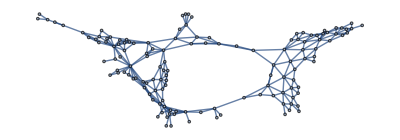

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
g=SimpleGraph[Subgraph[graph, Americas]]
```

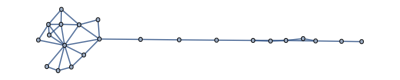

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
FindHamiltonianPath[g]
```

```mathematica
H={Entity["Country","Ecuador"],Entity["Country","Peru"],Entity["Country","Chile"],Entity["Country","Bolivia"],Entity["Country","Paraguay"],Entity["Country","Argentina"],Entity["Country","Uruguay"],Entity["Country","Brazil"],Entity["Country","FrenchGuiana"],Entity["Country","Suriname"],Entity["Country","Guyana"],Entity["Country","Venezuela"],Entity["Country","Colombia"],Entity["Country","Panama"],Entity["Country","CostaRica"],Entity["Country","Nicaragua"],Entity["Country","Honduras"],Entity["Country","ElSalvador"],Entity["Country","Guatemala"],Entity["Country","Belize"],Entity["Country","Mexico"],Entity["Country","UnitedStates"],Entity["Country","Canada"]}
```

{Ecuador,Peru,Chile,Bolivia,Paraguay,Argentina,Uruguay,Brazil,French Guiana,Suriname,Guyana,Venezuela,Colombia,Panama,Costa Rica,Nicaragua,Honduras,El Salvador,Guatemala,Belize,Mexico,United States,Canada}

```mathematica
pos = CountryData[#, "CenterCoordinates"] &/@ H;
```

```mathematica
GeoGraphics[{Thick, Red, GeoPath[pos]}]
```

-Graphics-

```mathematica
Americas
```

{Uruguay,Brazil,Argentina,Bolivia,French Guiana,Paraguay,Suriname,Venezuela,Colombia,Guyana,Peru,Chile,Ecuador,Panama,Costa Rica,Nicaragua,Honduras,Guatemala,El Salvador,Belize,Mexico,United States,Canada}